## Classification Lineaire

Simple Lineaire:

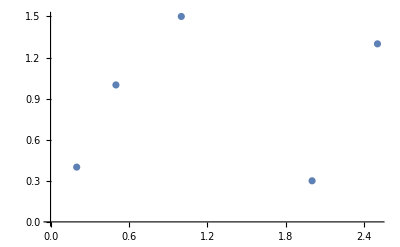

```mathematica
ListPlot[Table[Style[{{2.5,1.3},{2,0.3},{0.5,1},{1,1.5},{0.2,0.4}}]]]
```

```mathematica
Matrixlinear={{2.5,1.3}->"rond",{2,0.3}->"rond",{0.5,1}->"carre",{1,1.5}->"carre",{0.2,0.4}->"carre"};
```

```mathematica
c=Classify[Matrixlinear,Method->"LogisticRegression"]
```

ClassifierFunction[…]

```mathematica
c[{2.5,1.3},"Probabilities"]
```

<|carre→1.35999×10^-18,rond→1.|>

```mathematica
c[{1.15,0.5},"Probabilities"]
```

<|carre→0.551621,rond→0.448379|>

Perceptron Simple Couche : (Regression)

```mathematica
Matrixlinear2={{2.5,1.3}->1,{2,0.3}->1,{0.5,1}->0,{1,1.5}->0,{0.2,0.4}->0}; (* Mis en place de la base d'apprentissage)
```

```mathematica
p=Predict[Matrixlinear2]
```

```mathematica
(* Test sur la base d'apprentissage sortie attendue = 1)
```

```mathematica
p[{2.5,1.3}] 
p[{2,0.3}]
```

0.960838

1.02855

```mathematica
(* Test sur la base d'apprentissage sortie attendue = 0)
```

```mathematica
p[{0.5,1}]
p[{1,1.5}]
p[{0.2,0.4}]
```

-0.04494

0.059865

-0.00431283

```mathematica
(* Good ton modèle est capable de séparer tes données de la base d'apprentissage :) )
```

```mathematica
(* Il faut maintenant tester sur la base de test )
```

```mathematica
(* Test sur des exemple de test (inconnu pour le modèle) sortie attendue = 1)
```

```mathematica
p[{2.22,1.6}] 
p[{1.5,0.1}]
```

0.702027

0.820235

```mathematica
(* Test sur des exemple de test (inconnu pour le modèle) sortie attendue = 0)
```

```mathematica
p[{0.2,0.2}]
p[{0.6,1.3}]
p[{0.5,0.2}]
```

0.064694

-0.0929858

```mathematica
(* Nickel ! la base de test est correctement séparée )
```